```mathematica
heightCm = {0,5,10,15,40,80};
depthMS={40.53,59.47,71.2,86.59,94,106.55}; (*in mm*)
depthRS={42.26,46.57,48.55,64.14,80.65,94.62};depthCS={48.74,63.38,68.2,72.34,83.42,93.55};depthSL={0,41.95,41.58,41.49,57.52,74.21};
```

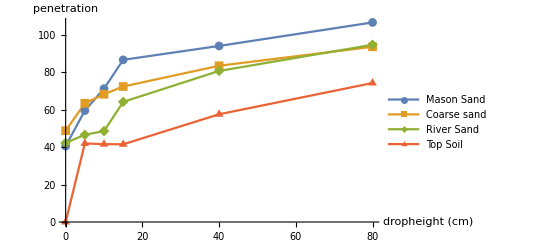

```mathematica
ListPlot[{Transpose[{heightCm,depthMS}],Transpose[{heightCm,depthCS}],
Transpose[{heightCm,depthRS}],Transpose[{heightCm,depthSL}]}
,AxesLabel->{"dropheight (cm)","penetration"},Joined->True,PlotMarkers->Automatic,PlotLegends->{"Mason Sand","Coarse sand","River Sand","Top Soil"}]
```